```mathematica
5^3/10^3
```

1/8

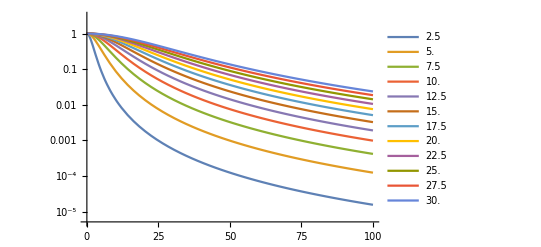

```mathematica
f[w_,d_,pow_]:=d^pow/Sqrt[d^2+w^2]^pow
LogPlot[Evaluate@Table[f[x,d],{d,2.5,30,2.5}],{x,0,100},PlotLegends->Table[d,{d,2.5,30,2.5}]]
```

```mathematica
sol3=Table[{d,Abs[x/.First[Solve[f[x,d,3]==0.01]]]},{d,0.01,30.01,0.1}];
sol2=Table[{d,Abs[x/.First[NSolve[f[x,d,2]==0.01]]]},{d,0.01,30.01,0.1}];
```

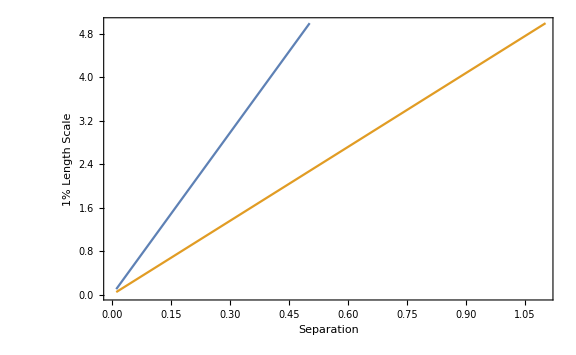

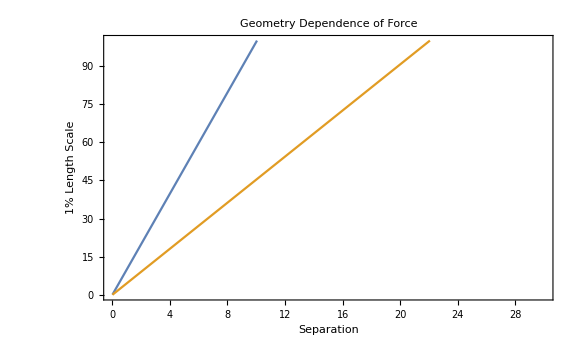

```mathematica
p2=ListLinePlot[{sol2,sol3},PlotRange->{{0,1.1},{0,5}},Frame->True,FrameLabel->{"Separation","1% Length Scale"}]
p1=ListLinePlot[{sol2,sol3},PlotRange->{0,100},Frame->True,FrameLabel->{"Separation","1% Length Scale"},PlotLabel->"Geometry Dependence of Force",ImageSize->Large]
```

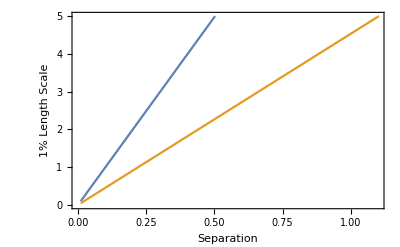
-Graphics-
-Graphics-

```mathematica
Graphics[{First[p1],Inset[p2,{22,30},Automatic,Scaled[.55]]},Options[p1]]
```